```mathematica
<<Indivaria`Game`
```

```mathematica
Game6[10^4,4,2,48,10,{0.3,0.2,2000*Vblood},{48,144,220,240},{0.5,0.001,26,48,0.5,0.04,48,168},{{144,200},1,1,200,{6.5,25.,0.0,99.0},{2.,1000,0.2}},480,3]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\works\Indivaria\Indivaria

```mathematica
IDVL["mod1_0.in"]
```

******INDIVARIA*****

model: 1.

outform: 3

********************

model: 1.

initn: 2.30*10^11

pmr: 10

mu: 10

sigma: 5

lifecycle: 48

killzone: {{6,26},{27,38},{39,44}}

concfile: P002.csv

everyh: 24

ndrug: 7

gamma: {5.5,5.5,5.5}

ec50: {20.0,20.0,20.0}

emin: {0.0,0.0,0.0}

emax: {99.99,99.99,99.99}

1/alpha: 5.5

lim: 8.

outform: 3

Total time: 240

intersection: {{62},{239}}

prr24: 764.308

prr48: 251.097

clearance time: 66

pmin(log10): 4.75107

recrudescence time: 240

{240,{{62},{239}},764.308,251.097,66,4.75107,240}

******INDIVARIA*****

model: 1.1

outform: 1

********************

model: 1.1

parafile: paraP002.csv

concfile: P002.csv

initn: 6.02*10^11

pmr: 12

mu: 13

sigma: 8

lifecycle: 48

killzone: {{6,20},{21,38},{39,44}}

everyh: 24

ndrug: 7

gamma: {8.31521,3.96412,3.96412}

ec50: {38.2193,0.662235,0.662235}

emin: {0.0,0.0,0.0}

emax: {99.9779,99.99,99.99}

1/alpha: 7.78339

outform: 1

runmax: 96

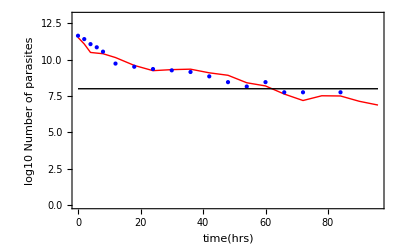

```mathematica
IDVL["mod1_1.in"]
```

```mathematica
IDVL["model1_2.in"]
```

******INDIVARIA*****

model: 1.2

outform: 0

********************

model: 1.2

parafile: paraP002.csv

concfile: P002.csv

runsteps: 50

outname: testP002

outform: 0

testP002.csv exists already.

$Aborted

```mathematica
IDVL["mod1_3.in"]
```

******INDIVARIA*****

model: 1.3

outform: 2

********************

model: 1.3

initn: 6.02*10^11

pmr: 12

mu: 13

sigma: 8

lifecycle: 48

concfile: P002.csv

everyh: 24

ndrug: 7

ec50: 38.2193

runmax: 70

dorfrac: 0.05

dortime: 7

outform: 2

******INDIVARIA*****

model: 1.3

outform: 2

********************

model: 1.3

initn: 6.02*10^11

pmr: 12

mu: 13

sigma: 8

lifecycle: 48

concfile: P002.csv

everyh: 24

ndrug: 7

ec50: 38.2193

runmax: 70

dorfrac: 0.05

dortime: 7

outform: 2

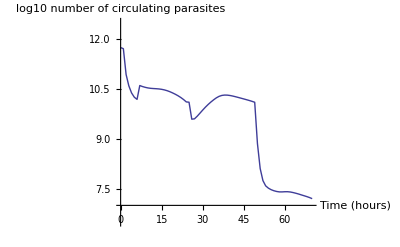

```mathematica
ListLinePlot[IDVL["mod1_3.in"],PlotRange->{6.5,12.5},FrameLabel->{"Time (hours)","Log10 Observed Parasites"},Joined->True,AxesLabel->{"Time (hours)","log10 number of circulating parasites"}]
```

******INDIVARIA*****

model: 1.4

outform: 2

********************

model: 1.4

initn: 6.02*10^4

lifecycle: 48

mu: 13

sigma: 8

pmr: 12

endage: 26

runmax: 240

outform: 2

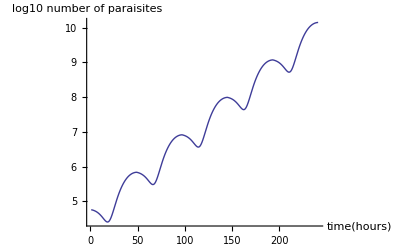

```mathematica
ListPlot[IDVL["mod1_4.in"],Joined->True,AxesLabel->{"time(hours)","log10 number of paraisites"}]
```

```mathematica
lsout=IDVL["mod1_5.in"];
```

******INDIVARIA*****

model: 1.5

outform: 0

********************

model: 1.5

lambda: 1.

mu: 0.00833

beta: 0.1

alpha: 0.2

r: 16.

d: 72

initx: 10000

inity: 1.

inits: 0.

runsteps: 600

stepsize: 0.1

outform: 0

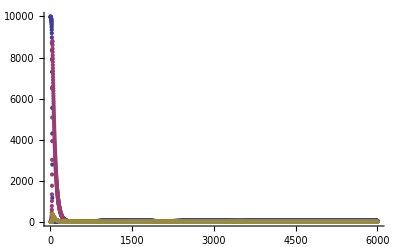

```mathematica
ListPlot[{lsout[[All,2]],lsout[[All,3]],lsout[[All,4]]}]
```

```mathematica
lsout=IDVL["mod1_6.in"];
```

******INDIVARIA*****

model: 1.6

outform: 0

********************

model: 1.6

initxy: {1,1}

initd: {1,1}

r: 4.

ps: {0.00001,0.001}

runsteps: 50

outform: 0

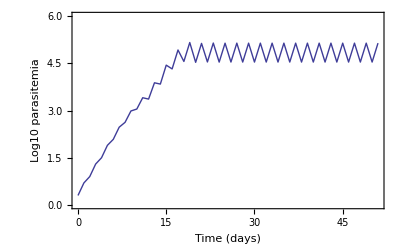

```mathematica
ls=Table[{lsout[[i,1]],Log10@lsout[[i,4]]},{i,1,Length@lsout}];
ListPlot[ls,Joined->True,PlotRange->{0,6},Frame->{True,True,False,False},FrameLabel->{"Time (days)","Log10 parasitemia"}]
```

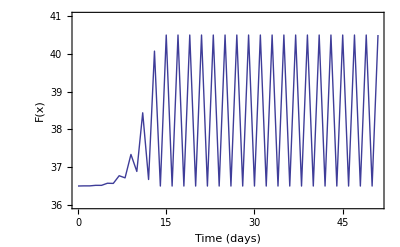

```mathematica
ls=Table[{lsout[[i,1]],lsout[[i,5]]},{i,1,Length@lsout}];
ListPlot[ls,Joined->True,PlotRange->{36,41},Frame->{True,True,False,False},FrameLabel->{"Time (days)","F(x)"}]
```

```mathematica
lsout=IDVL["mod1_7.in"];
```

******INDIVARIA*****

model: 1.7

outform: 0

********************

model: 1.7

initx: {1,1,1,1}

r: 16

h: 0.05

initd: {1,1,1,1}

inits: {0.00001,0.00002,0.0001,0.001}

runsteps: 50

outform: 0

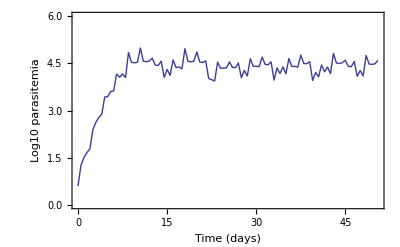

```mathematica
ls=Table[{lsout[[i,1]],Log10@lsout[[i,3]]},{i,1,Length@lsout}];
ListPlot[ls,Joined->True,PlotRange->{0,6},Frame->{True,True,False,False},FrameLabel->{"Time (days)","Log10 parasitemia"}]
```

```mathematica
lsout=IDVL["mod1_8.in"];
```

******INDIVARIA*****

model: 1.8

outform: 0

********************

model: 1.8

initn: {1000,200}

lambdals: {0.0309,0.0438}

muls: {0.1,0.25}

r: 8.3

runsteps: 60

stepsize: 0.1

outform: 0

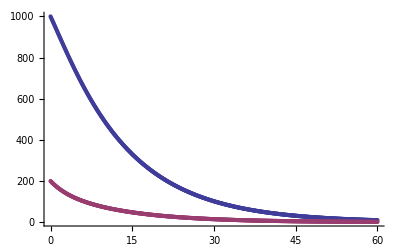

```mathematica
ListPlot[{lsout[[All,{1,2}]],lsout[[All,{1,3}]]},PlotRange->All]
```

```mathematica
ListPar[1.9,0]
```

{model,initn,pmr,mu,sigma,lifecycle,killzone,concfile,everyh,ndrug,gamma,ec50,emin,emax,1/alpha,runmax,dorfrac,dortime,outform}

```mathematica
lsout=IDVL["mod1_9.in"];
```

******INDIVARIA*****

model: 1.9

outform: 2

********************

model: 1.9

initn: 2.30*10^11

pmr: 10

mu: 10

sigma: 5

lifecycle: 48

killzone: {{6,26},{27,38},{39,44}}

concfile: P002.csv

everyh: 24

ndrug: 7

gamma: {5.5,5.5,5.5}

ec50: {20.0,20.0,20.0}

emin: {0.0,0.0,0.0}

emax: {99.99,99.99,99.99}

1/alpha: 5.5

runmax: 100

dorfrac: 0.02

dortime: 120

outform: 2

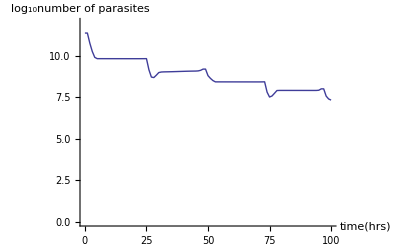

```mathematica
ListPlot[lsout,Joined->True,AxesLabel->{"time(hrs)","log_10number of parasites"},PlotRange->{0,12}]
```

******INDIVARIA*****

model: 2.

outform: 2

********************

model: 2.

initn: 2.30*10^11

pmr: 10

mu: 10

sigma: 5

lifecycle: 48

killzone: {{6,26},{27,38},{39,44}}

concfile: P002.csv

everyh: 24

ndrug: 7

gamma: {5.5,5.5,5.5}

ec50: {20.0,20.0,20.0}

emin: {0.0,0.0,0.0}

emax: {99.99,99.99,99.99}

1/alpha: 5.5

runmax: 100

dorfrac: 0.02

dortime: 120

dormu: 10

dorsig: 5

outform: 2

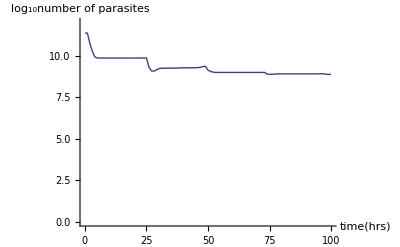

```mathematica
lsout=IDVL["mod2_0.in"];
ListPlot[lsout,Joined->True,AxesLabel->{"time(hrs)","log_10number of parasites"},PlotRange->{0,12}]
```

******INDIVARIA*****

model: 2.1

outform: 0

********************

model: 2.1

p0: 12.

a: 1.15

k: 0.036

k1: 3.45

c0: 1200

gamma: 2.5

c50: 665.4

outform: 0

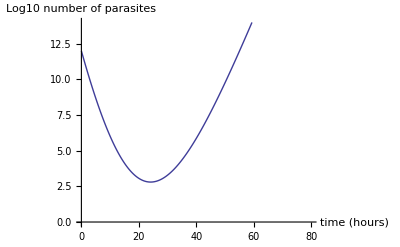

```mathematica
lsout=IDVL["mod2_1.in"];
ListPlot[lsout,Joined->True,PlotRange->{0,14},AxesLabel->{"time (hours)","Log10 number of parasites"}]
```

******INDIVARIA*****

model: 2.2

outform: 0

********************

model: 2.2

p0: 12.

a: 1.15

k: 0.036

k1: 3.45

c0: 1200

gamma: 2.5

c50: 665.4

mic: 504.3

outform: 0

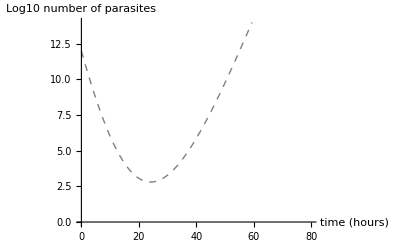

```mathematica
lsout=IDVL["mod2_2.in"];
ListPlot[lsout,Joined->True,PlotRange->{0,14},AxesLabel->{"time (hours)","Log10 number of parasites"},PlotStyle->{Dashed,Gray}]
```

******INDIVARIA*****

model: 2.3

outform: 1

********************

model: 2.3

parafile: paraP002.csv

concfile: P002.csv

initn: 6.02*10^11

pmr: 12

mu: 13

sigma: 8

lifecycle: 48

everyh: 24

ndrug: 7

ec50: 38.2193

dorfrac: 0.05

dortime: 7

outform: 1

runmax: 96

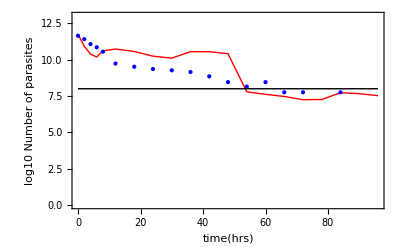

```mathematica
IDVL["mod2_3.in"]
```

******INDIVARIA*****

model: 2.6

outform: 1

********************

model: 2.6

parafile: paraP002.csv

concfile: P002.csv

initn: 2.30*10^11

pmr: 10

mu: 10

sigma: 5

lifecycle: 48

killzone: {{6,26},{27,38},{39,44}}

everyh: 24

ndrug: 7

gamma: {5.5,5.5,5.5}

ec50: {20.0,20.0,20.0}

emin: {0.0,0.0,0.0}

emax: {99.99,99.99,99.99}

1/alpha: 5.5

dorfrac: 0.02

dortime: 120

outform: 1

runmax: 96

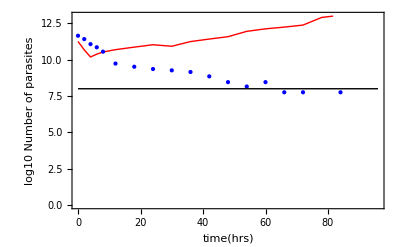

```mathematica
IDVL["mod2_6.in"]
```

```mathematica
SetDirectory@NotebookDirectory[]
```

D:\works\Indivaria\Indivaria

```mathematica
IDVL["mod2_71.in"]
```

```mathematica
SetDirectory["D:\\works\\ArtemisininResistance\\RERUN\\Pailin\\AS7"]
```

D:\works\ArtemisininResistance\RERUN\Pailin\AS7

```mathematica
IDVL["test.in"]
```

******INDIVARIA*****

model: 1.21

outform: 0

********************

model: 1.21

parafile: paraP002.csv

concfile: P002.csv

runsteps: 20

outname: out_P002

outform: 0

Creating an output file.

===Run no. 1===

runmax: 96

RMSD : 1.5369

The set of parameters is rejected.

===Run no. 2===

runmax: 96

RMSD : 6.07627

The set of parameters is rejected.

===Run no. 3===

runmax: 96

RMSD : 1.86394

The set of parameters is rejected.

===Run no. 4===

runmax: 96

RMSD : 1.30821

The set of parameters is rejected.

===Run no. 5===

runmax: 96

RMSD : 1.11338

The set of parameters is rejected.

===Run no. 6===

runmax: 96

RMSD : 0.859981

The set of parameters is collected.

===Run no. 7===

runmax: 96

RMSD : 1.64106

The set of parameters is rejected.

===Run no. 8===

runmax: 96

RMSD : 2.98377

The set of parameters is rejected.

===Run no. 9===

runmax: 96

RMSD : 1.91483

The set of parameters is rejected.

===Run no. 10===

runmax: 96

RMSD : 1.69338

The set of parameters is rejected.

===Run no. 11===

runmax: 96

RMSD : 15.4684

The set of parameters is rejected.

===Run no. 12===

runmax: 96

RMSD : 1.52315

The set of parameters is rejected.

===Run no. 13===

runmax: 96

RMSD : 1.84615

The set of parameters is rejected.

===Run no. 14===

runmax: 96

RMSD : 0.589397

The set of parameters is collected.

===Run no. 15===

runmax: 96

RMSD : 1.9418

The set of parameters is rejected.

===Run no. 16===

runmax: 96

RMSD : 1.0425

The set of parameters is rejected.

===Run no. 17===

runmax: 96

RMSD : 2.6004

The set of parameters is rejected.

===Run no. 18===

runmax: 96

RMSD : 16.0854

The set of parameters is rejected.

===Run no. 19===

runmax: 96

RMSD : 1.54515

The set of parameters is rejected.

===Run no. 20===

runmax: 96

RMSD : 1.47098

The set of parameters is rejected.

The program is finised.